# Parts of sets

How to calculate elements unique to an intersection of a venn diagram

Sumner Magurder, Jun. 24,  2018

A useful chart type is that of the Venn diagram (oddly not implemented in Mathematica). However, with many sets, it can be hard to figure out what elements are unique to which set. 
E.g. with sets A, B, C, D, E, F you might want to know A ∩ B ∩ D / C ∪ E ∪ F. 
Now it should be clear that there are 2^n comparisons that need to be made, so lets work out how to do visualize what elements belong to each Venn diagram component.

## Venn diagrams

Venn diagrams are a useful chart type for visualizing the interactions between sets (e.g. intersections, complements)

```mathematica
LinguisticAssistant
```

Failure[…]

-Graphics-

Output from Wolfram Alpha (calling via Mathematica fails as it can not be parsed. Also trying to use 6 sets fails on Wolfram Alpha).

Venn diagrams, while they look nice for 3 sets, get complicated fast (as there are 2^n parts). From the above example it is hard at first glance to find A ∩ B ∩ C ∩ D . So we are looking for a better way to visualize sets. The final chart will look like this:

Hang tight! This requires 64 comparisons.

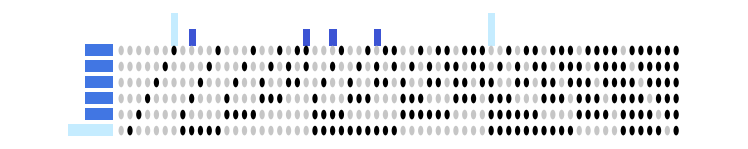

```mathematica
UpSetChart[sets]
```

## Define some sets

Lets define some sets

Rather than just a list of lists, we will use an association, so we can name our sets. This naming may be relevant later, especially when we want to visualize.

```mathematica
sets=<|
"a" -> {1,2,3,4,5},
"b" -> {1,2,5},
"c" -> {1,3,5},
"d" -> {1,4,5},
"e" -> {4,2,7},
"f" -> {7,8,10}
|>;
```

## Set some useful values

We will set some values so we do not have to constantly recompute them

```mathematica
numberOfSets=Length@sets;
setNames=Keys[sets];
```

It should be clear that the comparisons we need to make is equivalent to all possible subsets (2^n) of the names of our sets:

```mathematica
comparisonsToMake=Subsets[setNames]
```

{{},{a},{b},{c},{d},{e},{f},{a,b},{a,c},{a,d},{a,e},{a,f},{b,c},{b,d},{b,e},{b,f},{c,d},{c,e},{c,f},{d,e},{d,f},{e,f},{a,b,c},{a,b,d},{a,b,e},{a,b,f},{a,c,d},{a,c,e},{a,c,f},{a,d,e},{a,d,f},{a,e,f},{b,c,d},{b,c,e},{b,c,f},{b,d,e},{b,d,f},{b,e,f},{c,d,e},{c,d,f},{c,e,f},{d,e,f},{a,b,c,d},{a,b,c,e},{a,b,c,f},{a,b,d,e},{a,b,d,f},{a,b,e,f},{a,c,d,e},{a,c,d,f},{a,c,e,f},{a,d,e,f},{b,c,d,e},{b,c,d,f},{b,c,e,f},{b,d,e,f},{c,d,e,f},{a,b,c,d,e},{a,b,c,d,f},{a,b,c,e,f},{a,b,d,e,f},{a,c,d,e,f},{b,c,d,e,f},{a,b,c,d,e,f}}

Since we want to get elements unique to each SECTION of the venn diagram, where there is an implied /∪s∀s¬∈C where C is the set of sets we want to compare, it would be easier to work our way backwards from the the intersection of all sets, and then just ignored used values. So lets group our comparisons by the number of sets we are comparing.

Here we groupby the length of the number of sets in each comparison

```mathematica
groupped=GroupBy[comparisonsToMake,Length@#&]
```

<|0→{{}},1→{{a},{b},{c},{d},{e},{f}},2→{{a,b},{a,c},{a,d},{a,e},{a,f},{b,c},{b,d},{b,e},{b,f},{c,d},{c,e},{c,f},{d,e},{d,f},{e,f}},3→{{a,b,c},{a,b,d},{a,b,e},{a,b,f},{a,c,d},{a,c,e},{a,c,f},{a,d,e},{a,d,f},{a,e,f},{b,c,d},{b,c,e},{b,c,f},{b,d,e},{b,d,f},{b,e,f},{c,d,e},{c,d,f},{c,e,f},{d,e,f}},4→{{a,b,c,d},{a,b,c,e},{a,b,c,f},{a,b,d,e},{a,b,d,f},{a,b,e,f},{a,c,d,e},{a,c,d,f},{a,c,e,f},{a,d,e,f},{b,c,d,e},{b,c,d,f},{b,c,e,f},{b,d,e,f},{c,d,e,f}},5→{{a,b,c,d,e},{a,b,c,d,f},{a,b,c,e,f},{a,b,d,e,f},{a,c,d,e,f},{b,c,d,e,f}},6→{{a,b,c,d,e,f}}|>

And now we are almost ready to go. First we need to define to useful collection variables used (elements we do not consider unique) and intersections (where we store the values)

## Calculate unique intersections

```mathematica
used={}; (* elements here are no longer unique *)
intersections=<|{}->{}|>; (* cached values *)
For[n=numberOfSets,n>0,n--,
(* the intersections of all comparisions with n number of sets in them *)
intersectN = Intersection@@@(sets[#]&/@#&/@groupped[n]);
(* the intersections of all comparisions with n number of sets in them after we removed already used elements *)
uniqueAtN=Complement[#,used]&/@intersectN;
(* store the value with the name of the comparison *)
AppendTo[intersections, AssociationThread[groupped[n], uniqueAtN]];
(* update used *)
used=Union[used,Flatten[intersectN]];
];
```

## Visualize (simple)

Now that we have the elements unique to each part of the venn diagram, lets figure out a way to visualize them.

```mathematica
labels = (StringJoin/@(Riffle[#,","]&/@Keys@intersections));
elementsInIntersection=AssociationMap[First@#-> Length@Last@#&,intersections];
BarChart[
elementsInIntersection, 
ChartLabels->
Placed[labels,{{0.5,0},{0.9,1}},Rotate[#,(2/7) Pi]&],
ImageSize->Large,
ChartElementFunction->(Mouseover[Rectangle@@Transpose[#],
{
EdgeForm[Opacity[0.25]],
Rectangle@@Transpose[#],
Text[Style[#,Large, Bold,Red],#,Background->LightRed]&@@Transpose[#]
}
]&)
]
```

-Graphics-

That is nice, but we loose some information so lets make our own chart.
First lets get the max of each, we will need these for positioning and coloring

## Fancy Visualization

## Set some useful variables

```mathematica
maxI=Max[Length/@Values@intersections];
maxS=Max[Length/@Values@sets];
cd=ColorData["DeepSeaColors"];
```

Then lets define two rectangle types, ones that go horizontally to show the cardinality of the intersection (like the bar chart above) and another vertical one to show the cardinality of the set.

### Cardinality of intersection s

```mathematica
upsetIntersectionRectangle[numberOfSets_,intersections_, comparisonIndex_, comparsions_, pointRadius_,colorScale_,maxValue_]:=Module[
{
y=numberOfSets+pointRadius,
x=comparisonIndex-pointRadius,
c=comparsions[[comparisonIndex]],
v=intersections[comparsions[[comparisonIndex]]],
h=Length@intersections[comparsions[[comparisonIndex]]]
},
{
colorScale[h/maxValue],
Tooltip[
Rectangle[{x,y},{x+1-pointRadius,y+h}],
"Unique to: "<>ToString[c]<>"\nNumber of elements: "<>ToString[Length@v]<>"\nElements: "<>ToString[v]
]
}
];
```

### Cardinality of sets

```mathematica
upsetSetRectangle[setIndex_,setNames_,sets_, pointRadius_,colorScale_,maxValue_]:=Module[
{
y=setIndex-pointRadius,
x=-pointRadius,
s=setNames[[setIndex]],
v=sets[setNames[[setIndex]]],
w=Length@sets[setNames[[setIndex]]],
m=Max[Length/@Values@sets],
d
},
d=m-w;
{
colorScale[w/maxValue],
Tooltip[
Rectangle[{-m+d,y},{0,y+1-pointRadius}],
"Set: "<>ToString[s]<>"\nNumber of elements: "<>ToString[w]<>"\nElements: "<>ToString[v]
]
}
];
```

### Indicator for which set / intersection

```mathematica
upsetDisk[intersectionIndex_,setIndex_,comparisonsToMake_,setNames_, pointRadius_]:=Module[
{
whichSet=setNames[[setIndex]],
whichComparison=comparisonsToMake[[intersectionIndex]],
setInComparisonQ,
text
},

setInComparisonQ=MemberQ[whichComparison,whichSet];
text="Set: "<>ToString[whichSet]<>"\nIntersection: "<>ToString[whichComparison];

{
If[setInComparisonQ,Black,Lighter[Lighter[Gray]]],
Tooltip[Disk[{intersectionIndex,setIndex}, pointRadius],text]
}
]
```

### All together

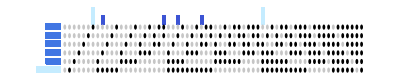

```mathematica
Graphics[
{
Table[
upsetIntersectionRectangle[numberOfSets,intersections, i, comparisonsToMake, 0.3,cd, maxI],
{i, Length@comparisonsToMake}
],

Table[
upsetDisk[i,j,comparisonsToMake,setNames, 0.3],
{j,numberOfSets},{i,Length@comparisonsToMake}
],

Table[
upsetSetRectangle[i,setNames,sets, 0.3,cd, maxS],
{i, Length@setNames}
]
}
]
```

## Parts of Venn Diagram chart (UpSet)

```mathematica
UpSetUniqueIntersections[sets_]:=Module[
{
numberOfSets,
setNames,
comparisonsToMake,
groupped,
used,
intersections,
n,intersectN,uniqueAtN
},

numberOfSets=Length@sets;
setNames=Keys[sets];
Print["Hang tight! This requires "<>ToString[2^(Length@setNames)]<>" comparisons."];
comparisonsToMake=Subsets[setNames];
groupped=GroupBy[comparisonsToMake,Length@#&];

used={};
intersections=<|{}->{}|>;
For[n=numberOfSets,n>0,n--,
(* the intersections of all comparisions with n number of sets in them *)
intersectN = Intersection@@@(sets[#]&/@#&/@groupped[n]);
(* the intersections of all comparisions with n number of sets in them after we removed already used elements *)
uniqueAtN=Complement[#,used]&/@intersectN;
(* store the value with the name of the comparison *)
AppendTo[intersections, AssociationThread[groupped[n], uniqueAtN]];
(* update used *)
used=Union[used,Flatten[intersectN]];
];

Return[
<|
"intersections"->intersections,
"numberOfSets"->numberOfSets,
"setNames"->setNames,
"comparisonsToMake"->comparisonsToMake
|>
]
]
UpSetChart[sets_]:=Module[
{
uniqueIntersections=UpSetUniqueIntersections[sets],
intersections,numberOfSets,setNames,comparisonsToMake,
maxI, maxS,cd
},

intersections=uniqueIntersections["intersections"];
numberOfSets=uniqueIntersections["numberOfSets"];
setNames=uniqueIntersections["setNames"];
comparisonsToMake=uniqueIntersections["comparisonsToMake"];
maxI=Max[Length/@Values@intersections];
maxS=Max[Length/@Values@sets];
cd=ColorData["DeepSeaColors"];

Graphics[
{
Table[
upsetIntersectionRectangle[numberOfSets,intersections, i, comparisonsToMake, 0.3,cd, maxI],
{i, Length@comparisonsToMake}
],

Table[
upsetDisk[i,j,comparisonsToMake,setNames, 0.3],
{j,numberOfSets},{i,Length@comparisonsToMake}
],

Table[
upsetSetRectangle[i,setNames,sets, 0.3,cd, maxS],
{i, Length@setNames}
]
}
]
]
```

Hang tight! This requires 64 comparisons.

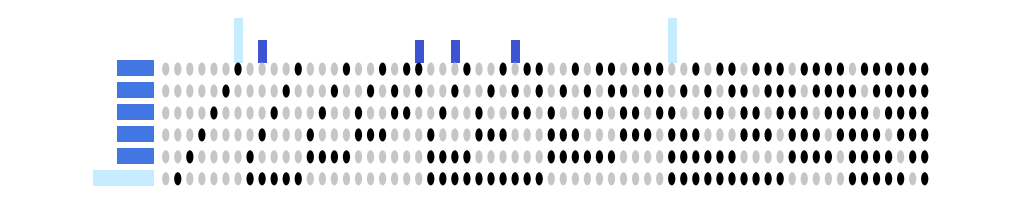

```mathematica
UpSetChart[sets]
```

```mathematica
sets=<|
"fruit"->{"banana","apple","watermelon","strawberry","grape"},
"red"->{"apple","watermelon"},
"tasty"->{"watermelon","grape"}
|>
```

<|fruit→{banana,apple,watermelon,strawberry,grape},red→{apple,watermelon},tasty→{watermelon,grape}|>

Hang tight! This requires 8 comparisons.

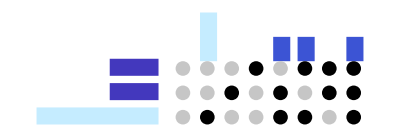

```mathematica
UpSetChart[sets]
```

```mathematica
sets=Association[Table[ToString@i -> RandomInteger[{0,100},RandomInteger[{2,15}]],{i,7}]];
```

Hang tight! This requires 128 comparisons.

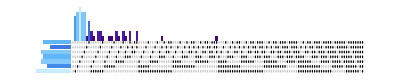

```mathematica
UpSetChart[sets]
```

## Further explorations

Name of a related topic for exploration

Name of another related topic for exploration (repeat as needed)

## Author contact information

sumner.magruder@uni-hamburg.zmnh.de

(We recommend using your wolfram ID, but any address where you would like to be contacted about this publication should work.)